```mathematica
$defaultTurtleState={{0,0},0,True};
```

This design is to support undo...

```mathematica
turtleProc[proc:{__}]:=Module[{turtleStates,}]
```

```mathematica
w[{a_,b_}]:=(Print[{a,b}];a)
```

```mathematica
Module[{list={0}},AppendTo[list,w[{#,Last[list]}]]&/@{1,2,3,4,5};list]
```

{1,0}

{2,1}

{3,2}

{4,3}

{5,4}

{0,1,2,3,4,5}

```mathematica
forward[state_List,distance_]:=If[state[[3]],Line[{state[[1]],{distance Cos[state[[2]]],distance Sin[state[[2]]]}+state[[1]]}],Nothing]
```

#### 2016/9/3

The most simple target is to generate the same figure as turtle, while no animation is required. This can be done with the forward function hjiaa wrote, after converting the python code to a custom Mathematica style instructions; or with the function AnglePath.

```mathematica
AnglePath[{{1.2,90.°},{2.1,130.°},{0.7,-85.°}}]
```

{{0.,0.},{7.34788×10^-17,1.2},{-1.60869,-0.149854},{-2.10367,0.345121}}

This function basically converts length-angle to point data.

With animation, the job can be done with Animate or Dynamic. Animate function has poor interactive ability, hence Dynamic is selected, for later extensions with mouse clicks/positions.

#### 20160904

```mathematica
hamstersBearSRC="import turtle
turtle.reset()

turtle.hideturtle()
turtle.speed(8)
turtle.up()
turtle.goto(0,-15)
turtle.down()
turtle.circle(5)

turtle.up()
turtle.goto(0,-100)
turtle.down()
turtle.circle(100)
turtle.up()
turtle.goto(-60,-2)
turtle.down()
turtle.circle(2)

turtle.up()
turtle.goto(60,-2)
turtle.down()
turtle.circle(2)

turtle.up()
turtle.goto(0,-15)
turtle.right(90)
turtle.down()
turtle.circle(7,120)
turtle.up()
turtle.goto(0,-15)
turtle.right(120)
turtle.down()
turtle.circle(-7,120)

turtle.up()
turtle.goto(-60,80)
turtle.down()
turtle.right(27.3)
turtle.circle(20,209)

turtle.up()
turtle.goto(60,80)
turtle.down()
turtle.left(85.6)
turtle.circle(-20,209)

turtle.done()
";
```

A python parser is needed, but it is too complicated. Therefore it will be developed only on demand.
This code example is very simple, there is even no indentation which needs converting to brackets (free of any looping constructs).

There are three things to achieve: extract all valid expressions by line, recognize convertible(valid) turtle functions and convert to the Mathematica intermediate functions, and deal with simple python expressions (numbers, arithmetic).

```mathematica
pyins=StringSplit[hamstersBearSRC,"\n"]/.{"":>Nothing," "..->""}
(*removes empty lines, removes extra spaces*)
```

{import turtle,turtle.reset(),turtle.hideturtle(),turtle.speed(8),turtle.up(),turtle.goto(0,-15),turtle.down(),turtle.circle(5),turtle.up(),turtle.goto(0,-100),turtle.down(),turtle.circle(100),turtle.up(),turtle.goto(-60,-2),turtle.down(),turtle.circle(2),turtle.up(),turtle.goto(60,-2),turtle.down(),turtle.circle(2),turtle.up(),turtle.goto(0,-15),turtle.right(90),turtle.down(),turtle.circle(7,120),turtle.up(),turtle.goto(0,-15),turtle.right(120),turtle.down(),turtle.circle(-7,120),turtle.up(),turtle.goto(-60,80),turtle.down(),turtle.right(27.3),turtle.circle(20,209),turtle.up(),turtle.goto(60,80),turtle.down(),turtle.left(85.6),turtle.circle(-20,209),turtle.done()}

```mathematica
(*check imports, returns module name(includes period)*)
modulename=Which[MemberQ[pyins,"from turtle import *"],"",MemberQ[pyins,"import turtle"],"turtle.",MemberQ[pyins,"import turtle as "~~_],Cases[pyins,"import turtle as "~~a_:>a<>"."]//First,True,Abort[]]
```

turtle.

```mathematica
supportedPyins=Select[pyins,StringMatchQ[Alternatives@@(modulename<>#<>"("~~___~~")"&/@{"down","up","circle","goto","left","right"})]]
```

{turtle.up(),turtle.goto(0,-15),turtle.down(),turtle.circle(5),turtle.up(),turtle.goto(0,-100),turtle.down(),turtle.circle(100),turtle.up(),turtle.goto(-60,-2),turtle.down(),turtle.circle(2),turtle.up(),turtle.goto(60,-2),turtle.down(),turtle.circle(2),turtle.up(),turtle.goto(0,-15),turtle.right(90),turtle.down(),turtle.circle(7,120),turtle.up(),turtle.goto(0,-15),turtle.right(120),turtle.down(),turtle.circle(-7,120),turtle.up(),turtle.goto(-60,80),turtle.down(),turtle.right(27.3),turtle.circle(20,209),turtle.up(),turtle.goto(60,80),turtle.down(),turtle.left(85.6),turtle.circle(-20,209)}

```mathematica
(*convert supported turtle instructions to mathematica expressions*)
(*numerical conversation is not safe. there is coflict between simple safe numerical conversation and support for basic numerical calculations inside function arguments*)
turtleIns=StringCases[modulename~~func__~~"("~~args___~~")":>Sequence[func,StringSplit[args,","]]]/@supportedPyins/.{args__String}:>(If[SyntaxQ[#],ToExpression[#],Nothing]&/@{args})
```

{{up,{}},{goto,{0,-15}},{down,{}},{circle,{5}},{up,{}},{goto,{0,-100}},{down,{}},{circle,{100}},{up,{}},{goto,{-60,-2}},{down,{}},{circle,{2}},{up,{}},{goto,{60,-2}},{down,{}},{circle,{2}},{up,{}},{goto,{0,-15}},{right,{90}},{down,{}},{circle,{7,120}},{up,{}},{goto,{0,-15}},{right,{120}},{down,{}},{circle,{-7,120}},{up,{}},{goto,{-60,80}},{down,{}},{right,{27.3}},{circle,{20,209}},{up,{}},{goto,{60,80}},{down,{}},{left,{85.6}},{circle,{-20,209}}}

After obtaining the Mathematica style instructions, then a function that converts these info to animation sequence is needed. 
First the job is to convert the instructions into Mathematica objects. This job can be done with Fold and sequentially changing turtle states, and Reap the graphics objects.

Here I present a naive design with Animate for basic functionality just to make above code work

```mathematica
Clear[tProc];
initState={{0,0},0,True};
(*initial orientation is x direction*)
tStateQ[state_]:=MatchQ[{{_?NumericQ,_?NumericQ},_?NumericQ,True|False}];
tProc[state_,{"up",{}}]:=Module[{s=state},s[[-1]]=False;s];
tProc[state_,{"down",{}}]:=Module[{s=state},s[[-1]]=True;s];
tProc[state_,{"goto",{x_,y_}}]:=Module[{s=state},If[state[[-1]],Sow[Line[{state[[1]],{x,y}}]]];s[[1]]={x,y};s];
tProc[state_,{"left",{angle_}}]:=Module[{s=state},s[[2]]+=angle;s[[2]]=Mod[s[[2]],360];s];
tProc[state_,{"right",{angle_}}]:=Module[{s=state},s[[2]]-=angle;s[[2]]=Mod[s[[2]],360];s];
tProc[state_,{"circle",{r_}}]:=Module[{s=state,center=state[[1]]+r{Cos[(state[[2]]+90)Degree],Sin[(state[[2]]+90)Degree]}},Sow[Circle[center,r]];s];
tProc[state_,{"circle",{r_,ext_}}]:=Module[{s=state,center=state[[1]]+r{Cos[(state[[2]]+90)Degree],Sin[(state[[2]]+90)Degree]}},Sow[Circle[center,Abs[r],(Sort[{0,Sign[r]ext}]+state[[2]]-Sign[r]90) Degree]];s[[2]]=Mod[s[[2]]+Sign[r]ext,360];s[[1]]=center+Abs[r]{Cos[s[[2]]Degree],Sin[s[[2]]Degree]};s];
```

```mathematica
res=Reap[Fold[tProc,initState,turtleIns]]
```

{{{59.2207,59.7134},208.3,True},{{Circle[{0,-10},5],Circle[{0,0},100],Circle[{-60,0},2],Circle[{60,0},2],Circle[{7,-15},7,{180 °,300 °}],Circle[{-7,-15},7,{240 °,360 °}],Circle[{-76.8302,69.1952},20,{0.570723,4.21846}],Circle[{76.8302,69.1952},20,{-1.07687,2.57087}]}}}

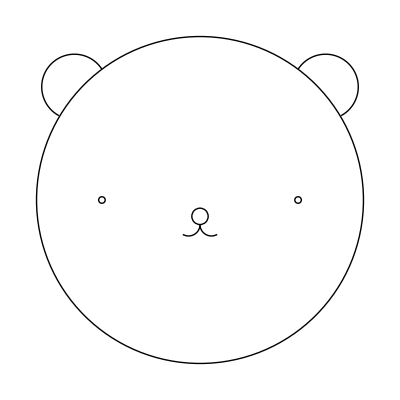

```mathematica
Graphics[res[[2]]]
```